# Implémentation des DLL C++

## Import de la DLL et test

```mathematica
Clear[pathToDll];
```

```mathematica
Needs["NETLink`"];
```

```mathematica
LoadNETType["System.Runtime.InteropServices.Marshal"]
```

NETType[System.Runtime.InteropServices.Marshal,17]

```mathematica
InstallNET[];
```

```mathematica
pathToDll="C:\\Users\\Clem\\Documents\\ESGI\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";
```

```mathematica
return42ExternFunc=DefineDLLFunction["return42",pathToDll,"int",{}];
```

```mathematica
return42ExternFunc[]
```

42

## Définitions Méthodes C++

```mathematica
Clear[createLinearModelClassif, linearFitClassificationRosenblatt, linearClassify, linearCreateAndFitRegression, linearPredict, createMlp, classify, fitClassification, predict, eraseMlp, getOutputsforRegression];
```

Perceptron Linéaire simple

## Création et suppression modèle

```mathematica
createLinearModelClassif = DefineDLLFunction["createLinearModelClassif", pathToDll, "System.IntPtr", {"int", "int"}];
```

```mathematica
eraseLinearModel = DefineDLLFunction["eraseLinearModel", pathToDll, "void", {"System.IntPtr"}];
```

## Classification Linéaire Rosenblatt

### Apprentissage

```mathematica
linearFitClassificationRosenblatt = DefineDLLFunction["linearFitClassificationRosenblatt", pathToDll, "int", {"System.IntPtr", "double[]", "int", "double[]", "int", "double"}];
```

### Classification

```mathematica
linearClassify =  DefineDLLFunction["linearClassify", pathToDll, "System.IntPtr", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

## Régression linéaire

### Apprentissage

```mathematica
linearCreateAndFitRegression = DefineDLLFunction["linearCreateAndFitRegression", pathToDll, "void", {"System.IntPtr", "double[]", "int", "int", "double[]","int"}];
```

### Predict

```mathematica
linearPredict = DefineDLLFunction["linearPredict", pathToDll, "void", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

Perceptron Multi - Couches

## Création et suppression du modèle

```mathematica
createMlp=DefineDLLFunction["createMlp",pathToDll,"System.IntPtr",{"int[]","int"}];
```

```mathematica
eraseMlp=DefineDLLFunction["eraseMlp",pathToDll,"void",{"System.IntPtr"}];
```

## Classification

### Apprentissage

```mathematica
fitClassification=DefineDLLFunction["fitClassification",pathToDll,"void",{"System.IntPtr","double[]","int","int","double[]","int"}];
```

### Classification

```mathematica
classify=DefineDLLFunction["classify",pathToDll,"void",{"System.IntPtr","double[]","int"}];
```

## Régression

### Apprentissage

```mathematica
fitRegression = DefineDLLFunction["fitRegression", pathToDll, "void", {"System.IntPtr", "double[]", "int", "double[]"}];
```

### Predict

```mathematica
predict=DefineDLLFunction["predict",pathToDll,"void",{"System.IntPtr","double[]","int"}];
```

```mathematica
getOutputsforRegression=DefineDLLFunction["getOutputsforRegression",pathToDll,"double",{"System.IntPtr"}];
```

RBF Naïf

RBF

## Cas de tests

Simple Linéaire Séparable

```mathematica
Clear[a,b,c,positivePointsL, negativePointsL, f];
```

```mathematica
a = RandomInteger[{-5; 5}];
b= RandomInteger[{-5; 5}];
c= RandomInteger[{-5; 5}];
```

```mathematica
f[x_] := -a/b*x+c/b
```

```mathematica
positivePointsL = Table[x= RandomReal[{-5, 5}]; {x, f[x] + RandomReal[{0.5, 2}]}, {i,1, 3}]
```

{{-4.18754,5.07707},{-3.52608,5.74671},{0.945631,0.496986}}

```mathematica
negativePointsL = Table[x = RandomReal[{-5, 5}];
{x, f[x]-RandomReal[{0.5, 2 }]}, {i,1,3}]
```

{{4.63709,-5.45435},{-1.26421,-0.237461},{4.1409,-5.79688}}

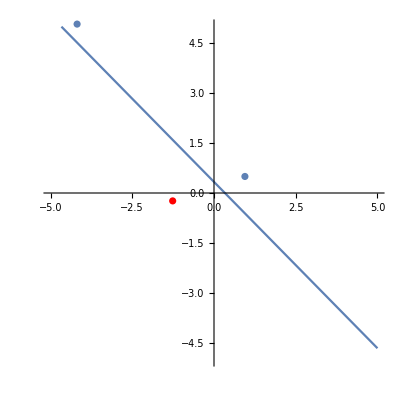

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],
ListPlot[negativePointsL, PlotStyle->Red],
ListPlot[positivePointsL]]
```

Simple non linéairement séparable

```mathematica
Clear[redPointsNL, bluePointsNL];
```

```mathematica
redPointsNL = {positivePointsL[[1]], positivePointsL[[2]], negativePointsL[[1]]}
bluePointsNL = {positivePointsL[[3]], negativePointsL[[2]], negativePointsL[[3]]}
```

{{-4.18754,5.07707},{-3.52608,5.74671},{4.63709,-5.45435}}

{{0.945631,0.496986},{-1.26421,-0.237461},{4.1409,-5.79688}}

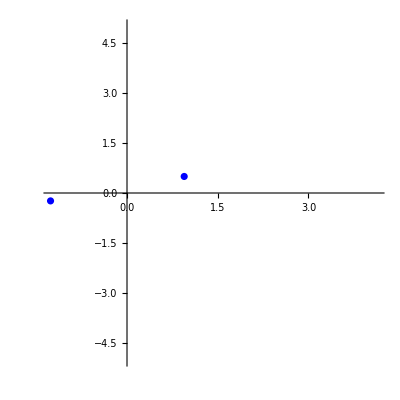

```mathematica
Show[ListPlot[bluePointsNL, PlotStyle->Blue,AspectRatio->1, PlotRange->{-5, 5}], ListPlot[redPointsNL, PlotStyle->Red]]
```

Cross

```mathematica
Clear[left,right,top, down];
```

```mathematica
left[x_] = (-1)*Abs[a*x];
right[x_] = Abs[a*x];
top [x_]= Abs[a];
down [x_]= (-1) * Abs[a];
```

```mathematica
rand = RandomReal[{-5,5}];
```

```mathematica
rightHighPoints = Table[x = rand;
{right[x]+RandomReal[{0.5,2}], top[x]+RandomReal[{0.5,2}]},{i,1,15}];
rightDownPoints = Table[x = rand;
{right[x]+RandomReal[{0.5,2}], down[x]-RandomReal[{0.5,2}]},{i,1,15}];
leftHighPoints = Table[x = rand;
{left[x]-RandomReal[{0.5,2}], top[x]+RandomReal[{0.5,2}]},{i,1,15}];
leftDownPoints = Table[x = RandomReal[{-5,5}];
{left[x]-RandomReal[{0.5,2}], down[x]-RandomReal[{0.5,2}]},{i,1,15}];
```

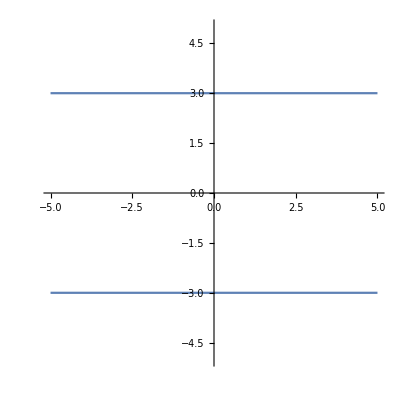

```mathematica
Show[Plot[left[x], {x, -5, 5}, PlotRange->{-5,5}, AspectRatio->1],
Plot[top[x], {x, -5, 5}], Plot[right[x], {x, -5, 5}], Plot[down[x], {x, -5, 5}],
ListPlot[rightDownPoints], ListPlot[rightHighPoints], ListPlot[leftDownPoints], ListPlot[leftHighPoints]]
```

XOR

```mathematica
Clear[a, Pmc, Xxor, Yxor,test]
```

```mathematica
a = RandomInteger[{-5, 5}]
red = {{a, -a}, {-a, a}}
blue = {{-a, -a},{a,a}}
```

1

{{1,-1},{-1,1}}

{{-1,-1},{1,1}}

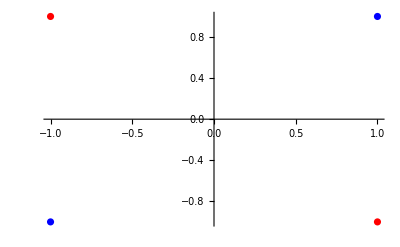

```mathematica
Show[ListPlot[red, PlotStyle-> Red],ListPlot[blue, PlotStyle->Blue]]
```

```mathematica
Xxor = {{-1,1},{1,-1},{1,1},{-1,-1}};
Yxor = {-1, -1, 1, 1}
```

{-1,-1,1,1}

## Utilisation méthodes

Simple Linéaire Séparable

```mathematica
Clear[modelLinear, XLinear, YLinear, XLineartest, XLineartest2, YLinear, YLineartest];
```

```mathematica
modelLinear = createLinearModelClassif[2,1];
```

```mathematica
XLinear=Flatten[{positivePointsL, negativePointsL}];
YLinear = {1,1,1, -1,-1,-1};
```

```mathematica
XLineartest = {XLinear[[1]], XLinear[[2]]};
YLineartest = {YLinear[[1]]};
```

```mathematica
linearFitClassificationRosenblatt[modelLinear, XLinear,12, YLinear,1000, 0.1];
```

```mathematica
YMarshaltest = NETNew["int[]", 1]
```

«NETObject[System.Int32[]]»

```mathematica
Marshal`Copy[linearClassify[modelLinear, XLineartest, 2, YLineartest, 1], YMarshaltest, 0, 1]
```

```mathematica
NETObjectToExpression[YMarshaltest]
```

{0}

```mathematica
XLineartest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
positive = Select[XLineartest2,linearClassify[modelLinear, #,2, YLineartest,1 ]== 1&]; 
negative =Select[XLineartest2,linearClassify[modelLinear, #,2, YLineartest,1 ]== -1&]
```

{}

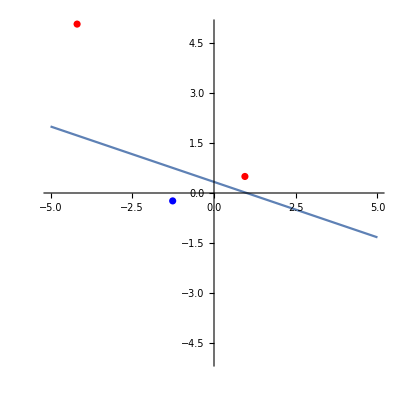

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

```mathematica
(*Clear[model, X, Y, Xtest, Xtest2, Y, Ytest];*)
```

```mathematica
managedTab = NETNew["int[]", 5]
LoadNETType["System.Runtime.InteropServices.Marshal"]
Marshal`Copy[funct, managedTab, 0, 5]
managedTab@GetValue[2]
```

«NETObject[System.Int32[]]»

NETType[System.Runtime.InteropServices.Marshal,17]

NET::methodargs: Improper arguments supplied for method named Copy.

$Failed

0

```mathematica
copyFromNetArray[array_] := Table[array@GetValue[i], {i, 0, array@Length-1}]
```

```mathematica
NETObjectToExpression[managedTab]
```

{0,0,0,0,0}